Mathematica  notebook  for  the  article {}.

# Definitions

```mathematica
Get[NotebookDirectory[]<>"SpinOperatorLibrary.m"]
```

```mathematica
EigensystemSorted[H_]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[H(*,Method->{"Banded"}*)];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,Map[Normalize,eig]}
]
EigenvaluesSorted[H_]:=EigensystemSorted[H][[1]]
EigenvectorsSorted[H_]:=EigensystemSorted[H][[2]]
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]}];
StylePts={PlotStyle->Black,PlotMarkers->{cross,0.04}};
```

```mathematica
<<MaTeX`
font={BaseStyle->{Black,FontFamily->"Times New Roman",FontSize->12},AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{Black,FontFamily->"Times New Roman",FontSize-> 12}};
```

```mathematica
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
```

# Models definition

```mathematica
(*Eq.7 from Mechanism of dynamical phase transition: ...*)
Lipkin[λ_,h_,n_]:=Re[(- λ)/n Jx[n].Jx[n]+h Jz[n]]
```

# Complexified fidelity

## Choose model and specify quench

```mathematica
(*1D Section of Lipkin model*)
H=Lipkin[#,1.`30,60]&;
(*Initial point and state*)
λI=7.`30;
levelI=1;
psiI=(EigenvectorsSorted[H[λI]][[levelI]]+EigenvectorsSorted[H[λI]][[levelI+1]])/(√2);
(*Final point*)
λF=2.`30;
```

```mathematica
dim=Length@H[1.]
```

61

## Define fidelity

```mathematica
eI= EigenvaluesSorted[H[λI]];
eigvF= EigenvectorsSorted[H[λF]];
eF= EigenvaluesSorted[H[λF]];
```

```mathematica
k=Abs[Conjugate[psiI].eigvF[[#]]]^2&/@Range[dim];
Z[β_,t_]:= Total[k[[#]]Exp[-eF[[#]](β+I t)]&/@Range[dim]];

βPred[i_,j_]:=1/(eF[[i]]-eF[[j]])Log[k[[i]]/k[[j]]]
βPredRadius[i_,j_]:=Total[k[[#]]Exp[-eF[[#]] βPred[i,j]]&/@Range[dim]]/(√Total[eF[[#]]^2 k[[#]]^2 Exp[-2 eF[[#]]βPred[i,j]]&/@Range[dim]])
tPred[i_,j_]:=Table[π/(eF[[i]]-eF[[j]])(2n+1),{n,-350,350}];
```

## Search for zeroes

Recursive  search  for zeroes of complexified function Z[t,β]->Z[Re[z],Im[z]] using  contour  integral.

```mathematica
Z[z_]:=Z[Re@z,Im@z]
(*Set area and recursion depth*)
zRange={-2.+0I,4+20I};
RecursionSteps=2;
```

```mathematica
(*Compute winding numbers by integrating along the rectangle border*)
ComputeWindingNumberRect[min_,max_]:=Module[{z0},
z0=(max+min)/2;
Re[1/(2π I)Quiet@ContourIntegrate[ND[Z[zp],zp,z,Scale->0.001,Terms->11]/Z[z],z∈Rectangle[{Re@min,Im@min},{Re@max,Im@max}],WorkingPrecision->30]]
]
```

```mathematica
SubdivideRect[{min_,max_}]:=Module[{subd,reMin,reMax,imMin,imMax,reQuarters,imQuarters,subdividedRectangles,subdividedRectanglesWinding,selected},
(*subdivide the edge of square into subd pieces*)
subd=8;

{reMin,reMax}=Re[{min,max}];
{imMin,imMax}=Im[{min,max}];
(*Calculate quarter points along real and imaginary axes*)
reQuarters=Subdivide[reMin,reMax,subd];
imQuarters=Subdivide[imMin,imMax,subd];

(*Generate subd^2 subrectangles*)subdividedRectangles=Flatten[Table[{reQuarters[[i]]+I imQuarters[[j]],reQuarters[[i+1]]+I imQuarters[[j+1]]},{i,1,subd},{j,1,subd}],1];
(*Compute winding numbers for each subrectangle*)
subdividedRectanglesWinding=Parallelize[ComputeWindingNumberRect@@@subdividedRectangles];
(*Select rectangles with non-zero winding numbers, set some reasonable threshold*)
selected=Pick[subdividedRectangles,#>0.3&/@subdividedRectanglesWinding];
Print["selected rectangles: ",selected];
selected
]
FindRectangles[rectangle_,depth_]:=Module[{rects},
If[depth>=RecursionSteps,
(*At max depth,return the rectangle*){rectangle},
(*Subdivide and continue recursively*)Print["entering depth: ",depth];
rects=SubdivideRect[rectangle];
FindRectangles[#,depth+1]&/@rects
]
]
RootsFromRectangles[rectangles_]:=Map[(#[[1]]+#[[2]])/2&,rectangles];
ExtractCoordinates[list_]:=Cases[list,{x_,y_}/;NumericQ[x]&&NumericQ[y],Infinity]
```

```mathematica
(*Initial rectangle over which to find zeroes*)
initialRect={zRange[[1]],zRange[[2]]};
(*Find rectangles containing zeros*)
rectanglesWithZeros=FindRectangles[initialRect,0];
```

```mathematica
rectanglesWithZeros=ExtractCoordinates[rectanglesWithZeros];
roots=RootsFromRectangles[rectanglesWithZeros];
```

```mathematica
Export[NotebookDirectory[]<>"data/rectanglesWithZeros_N=60.m",rectanglesWithZeros];
Export[NotebookDirectory[]<>"data/roots_N=60.m",roots];
```

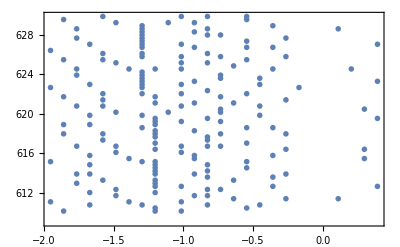

```mathematica
ListPlot[{Re@#,Im@#}&/@roots,PlotStyle->PointSize[0.01],Frame->True,Axes->False]
```

#### Increasing precision

We  can  increase the recursion depth starting from the pre

```mathematica
rectanglesWithZeros=Import[NotebookDirectory[]<>"data/rectanglesWithZeros_N=60.m"];
Length[rectanglesWithZeros]
rectanglesWithZerosNew1=FindRectangles[#,1]&/@rectanglesWithZeros
```

```mathematica
rectanglesWithZerosNew=ExtractCoordinates@rectanglesWithZerosNew;
```

```mathematica
rootsNew=RootsFromRectangles@rectanglesWithZerosNew;
```

```mathematica
ListPlot[{Re@#,Im@#}&/@rootsNew,PlotStyle->PointSize[0.01],Frame->True,Axes->False]
```

```mathematica
Export[NotebookDirectory[]<>"data/rectanglesWithZeros_N=60.m",rectanglesWithZerosNew];
Export[NotebookDirectory[]<>"data/roots_N=60",rootsNew];
```

## Select intersections

```mathematica
(*From two lists Subscript[eF, j] and Subscript[k, j] we can select those combinations {i,j} which undergo some condition*)
```

```mathematica
c=0.1 ;
```

```mathematica
Δ[i_,j_]:=eF[[i]]-eF[[j]]
(*first condition*)
hood1[i_,j_]:=AllTrue[Table[k[[n]]<k[[i]](k[[i]]/k[[j]])^(-Δ[i,n]/Δ[i,j]),{n,DeleteElements[Range[dim],{i,j}]}],TrueQ]
cond2[i_,j_]:=Table[Abs[k[[n]]/k[[i]](k[[i]]/k[[j]])^(Δ[i,n]/Δ[i,j])-1]>c,{n,DeleteElements[Range[dim],{i,j}]}];
hood2[i_,j_]:=AllTrue[cond2[i,j],TrueQ]
```

```mathematica
bb[i_,j_]:=1/Δ[i,j] Log[k[[i]]/k[[j]]]
tt[i_,j_,n_]:=1/Δ[i,j] I π(2n+1)
z[i_,j_,n_]:=bb[i,j]+tt[i,j,n]
Δβn[i_,j_,n_]:=Total[Abs[k[[#]]Exp[-eF[[#]]z[i,j,n]]]&/@Range[dim]]/Total[Abs[eF[[#]]k[[#]]Exp[-eF[[#]]z[i,j,n]]]&/@Range[dim]]
Δβ[i_,j_]:= Mean[Δβn[i,j,#]&/@Range[10000]]
```

```mathematica
SelectByHood[pairs_,hood_]:=Module[{pairsHoodTrue},
pairsHoodTrue=Flatten@Position[hood@@@pairs,True];
(*return pairs corresopnding to the condition*)
pairs[[#]]&/@pairsHoodTrue
]
```

```mathematica
(*define all pairs*)
pairs=Select[Subsets[Range[dim],{2}],OrderedQ];
(*return pairs undergoing the condition defined by a function, such as hood[i,j]*)
pairsHood1=SelectByHood[pairs,hood1]
pairsHood2=SelectByHood[pairsHood1,hood2]
```

{{1,2},{2,4},{4,6},{6,8},{8,10},{10,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{22,23},{23,24},{24,25},{25,26},{26,27},{27,28},{28,29},{29,30},{30,31},{31,32},{32,33},{33,34},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,42},{42,43},{43,44},{44,45},{45,46},{46,47},{47,48},{48,49},{49,50},{50,51},{51,52},{52,53},{53,54},{54,55},{55,56},{56,57},{57,58},{58,59},{59,60},{60,61}}

{{1,2},{54,55},{55,56},{56,57},{57,58},{58,59},{59,60},{60,61}}

```mathematica
(*check which energy levels caused the {i,j} combination to drop out from pairsHood1 to pairsHood2*)
pairsHood2False=Module[{condResult,dict},condResult=cond2@@@pairsHood1;
dict=pairsHood1[[#]]->Flatten[Position[condResult[[#]],False]]&/@Range[Length[pairsHood1]];
Select[dict,#[[2]]=!={}&]]
```

{{2,4}→{1,2},{4,6}→{3,4},{6,8}→{5,6},{8,10}→{7,8,10,12,13,14},{10,15}→{7,8,9,11,13,14,15},{15,16}→{7,8,9,10,12,14,15},{16,17}→{14,15,16,17},{17,18}→{16,17,18},{18,19}→{16,17,18,19},{19,20}→{17,18,19,20},{20,21}→{18,19,20,21},{21,22}→{19,20,21,22},{22,23}→{20,21,22,23},{23,24}→{21,22,23,24},{24,25}→{22,23,24,25},{25,26}→{23,24,25,26},{26,27}→{24,25,26,27},{27,28}→{25,26,27,28},{28,29}→{26,27,28,29},{29,30}→{27,28,29,30},{30,31}→{28,29,30,31},{31,32}→{29,30,31,32},{32,33}→{30,31,32,33},{33,34}→{31,32,33},{34,35}→{32,33,34},{35,36}→{33,34,35},{36,37}→{35,36},{37,38}→{36,37},{38,39}→{37,38},{39,40}→{38,39},{40,41}→{39,40},{41,42}→{40,41},{42,43}→{41,42},{43,44}→{42,43},{44,45}→{43,44},{45,46}→{44,45},{46,47}→{45,46},{47,48}→{46,47},{48,49}→{47,48},{49,50}→{48,49},{50,51}→{49,50},{51,52}→{50,51},{52,53}→{51,52},{53,54}→{52}}

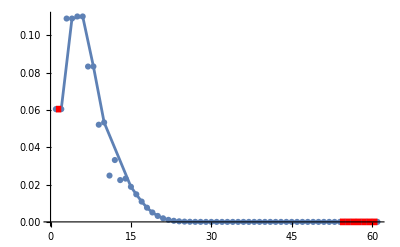

```mathematica
pairsLine[{i_,j_}]:={{i,k[[i]]},{j,k[[j]]}}
Show[{
ListPlot[k]
,Show[ListLinePlot[pairsLine[#]]&/@pairsHood1]
,Show[ListLinePlot[pairsLine[#],PlotStyle->{Dashed,Red,Thickness[0.012]}]&/@pairsHood2]
}]
```

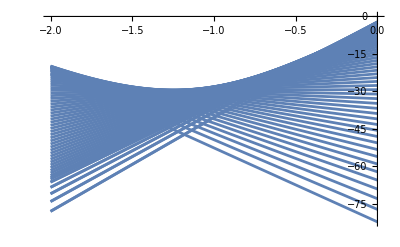

```mathematica
Plot[-eF[[#]]x +Log[k[[#]]]&/@Range[dim],{x,-2,0}]
```

## Plot

```mathematica
zRange={-2+0I,1+630I};
tSplit1=13; (*bottom plot maximum*)
tSplit2=610; (*top plot minimum*)

resolution=200; (*PlotPoints in DensityPlot*)
```

```mathematica
rootsbottom=Import[NotebookDirectory[]<>"data/roots_N=60.m"];
rootstop=Import[NotebookDirectory[]<>"data/roots_N=60.m"];
roots=Join[rootsbottom,rootstop];
Dimensions[roots]
```

{319}

```mathematica
(*calculating betaij precitions along with their confidence intervals, from combinations of i,j selected by some hood condition*)
{betas1,betas2}=Map[βPred@@@#&,{pairsHood1,pairsHood2}];
{ts1,ts2}=Map[tPred@@@#&,{pairsHood1,pairsHood2}];
{betasRadius1,betasRadius2}=Map[βPredRadius@@@#&,{pairsHood1,pairsHood2}];
```

```mathematica
{βRange,tRange}={Re@zRange,Im@zRange};
ZTab1=Flatten[ParallelTable[{β,t,Log@Abs@Z[β,t]},{β,βRange[[1]],βRange[[2]],(βRange[[2]]-βRange[[1]])/resolution},{t,tRange[[1]],tSplit1,(tSplit1-tRange[[1]])/resolution}],1];
ZTab2=Flatten[ParallelTable[{β,t,Log@Abs@Z[β,t]},{β,βRange[[1]],βRange[[2]],(βRange[[2]]-βRange[[1]])/resolution},{t,tSplit2,tRange[[2]],(tRange[[2]]-tSplit2)/resolution}],1];
```

```mathematica
ZPlotGen[tab_,plotlegends_]:=
Show[{
(*background - complex fidelity*)
ListDensityPlot[tab,
PlotRange->All,ColorFunction->"BlueGreenYellow",
PlotRangePadding->0,FrameLabel->MaTeX/@{"\\beta","t"},Evaluate@font,
Axes->False,
PlotLegends->plotlegends
]

(*predictions*)
,Table[ListPlot[{betas1[[i]],#}&/@ts1[[i]],PlotStyle->{Opacity[0.1],Black},Evaluate@StylePts],{i,1,Length@betas1}]
,Table[ListPlot[{betas2[[i]],#}&/@ts2[[i]],Evaluate@StylePts],{i,1,Length@betas2}]
(*line predictions*)
,Table[ListLinePlot[{{betas1[[i]],tSplit2},{betas1[[i]],Im@zRange[[2]]}},PlotStyle->{Thickness[0.0005],Black}],{i,1,Length@betas1}]
,Table[ListLinePlot[{{betas2[[i]],tSplit2},{betas2[[i]],Im@zRange[[2]]}},PlotStyle->{Thickness[0.001],Black,Opacity[0.1]}],{i,1,Length@betas2}]


(*approximately found zeroes using contour integral*)
,ListPlot[{Re@#,Im@#}&/@roots,PlotStyle->{White,PointSize[0.01]}]
},AspectRatio->2/5];
```

```mathematica
fidelityPlot=Quiet@ResourceFunction["PlotGrid"][{
{ZPlotGen[ZTab2,False]},
{ZPlotGen[ZTab1,Automatic]}
},"MergeAxes"->"ZigZag",Spacings->{0,5},ImageSize->455]
```

-Graphics-

```mathematica
spec=Plot[EigenvaluesSorted[H[λ]],{λ,0.,7.5},Axes->False,Frame->True,ImageSize->Medium,AspectRatio->1,FrameLabel->MaTeX/@{"h","E"},PlotRangePadding->0,PlotStyle->{Black,Thickness[0.004]}];
```

```mathematica
spectrumPlot=Show[{
spec,
ListPlot[{{λI,eI[[levelI]]}},PlotStyle->{PointSize[0.04],Green}],
Table[ListPlot[{{λF,eF[[i]]}},PlotStyle->{PointSize[k[[i]]^(1/2)0.1],Green,Opacity[k[[i]]^(1/20)]}],{i,1,dim}]
}];
kPlot=ListPlot[k[[#]]&/@Range[dim],PlotRange->{{0.5,dim+0.5},{Min@k-0.01,Max@k+0.01}},Axes->False,Frame->True,ImageSize->Medium,AspectRatio->1,FrameLabel->MaTeX/@{"i","k_i"},PlotRangePadding->0,FrameTicks->{{Automatic,None},{Range[5,dim,5],None}},PlotStyle->{Black,PointSize[0.02]}];
```

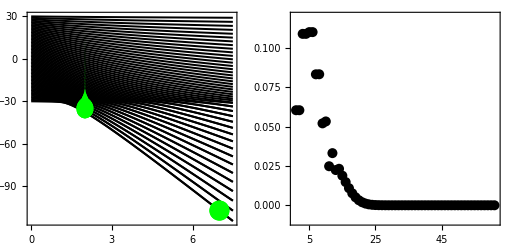

```mathematica
plot12=GraphicsRow[{spectrumPlot,kPlot},ImageSize->510]
```

```mathematica
Export[NotebookDirectory[]<>"img/fidelity_zeroes_N=60.pdf",fidelityPlot,"AllowRasterization"->True,ImageResolution->2000];
```

```mathematica
Export[NotebookDirectory[]<>"img/fidelity_zeroes_N=60_spectrum.pdf",plot12,"AllowRasterization"->True,ImageResolution->2000];
```